## L=4*4

## vary density, β=16

```mathematica
ndca={1.3,1.25,1.2,1.15,1.1,1.05,1,0.95,0.9,0.85,0.8,0.75,0.7};
```

```mathematica
nd={0.7354376160262402,0.7241233568219207,0.7120547517626896,0.6993907037191383,0.6863372215573458,0.6732275044022352,0.6598360778876292,0.6283490715651128,0.5872703565672718,0.5507716540871488,0.5151744840236205,0.48044072804174864,0.44590183572730585};nL={0.544457497,0.508441956,0.472807325,0.437569194,0.40272501,0.368259028,0.337965433,0.32084615,0.308303558,0.29540513,0.281566157,0.26720163,0.252164243};
nLbar={0.015847224,0.013893527,0.01207131,0.01040214,0.008990493,0.008012241,0.00765234,0.007413335,0.006702764,0.005968713,0.005305313,0.00479299,0.004449709};
ndvsn=Table[{ndca[[i]],nd[[i]]/ndca[[i]]},{i,1,13}];nLvsn=Table[{ndca[[i]],nL[[i]]/ndca[[i]]},{i,1,13}];
nLbarvsn=Table[{ndca[[i]],nLbar[[i]]/ndca[[i]]},{i,1,13}];
```

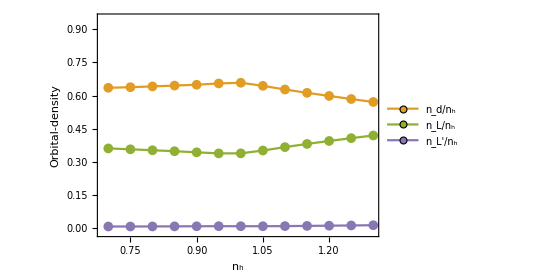

```mathematica
orbitalvsn=ListPlot[{nCuvsn,nLvsn,nLbarvsn},PlotLegends->Placed[LineLegend[{"n_d/n_h","n_L/n_h","n_L'/n_h"},LabelStyle->{FontFamily->"Arial",15},LegendLayout->{"Row",1},LegendMarkerSize->11],{0.5,0.93}],PlotMarkers->{Graphics[Disk[]],10},Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"Arial"},PlotRange->{Automatic,{-0.02,0.95}},PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.528488, 0.470624, 0.701351]},FrameLabel->{Subscript[n,h],"Orbital-density"},LabelStyle->{FontFamily->"Arial"},Joined->True,PlotStyle->{Red,Green,Blue}]
```

```mathematica
Export["/Users/cosdis/Desktop/threeband_project/MS_pairing_structure/orbitalvsn.pdf",orbitalvsn,"PDF"];
```